```mathematica
pp210a=Import["/Users/Micah/Documents/JerryDuty/eikexp/pp210a.csv"];
pp210a=Transpose[{pp210a[[All,1]],pp210a[[All,2]]+I*pp210a[[All,3]]}];
```

```mathematica
pp210b=Import["/Users/Micah/Documents/JerryDuty/eikexp/pp210b.csv"];
pp210b=Transpose[{pp210b[[All,1]],pp210b[[All,2]]+I*pp210b[[All,3]]}];
```

```mathematica
pp210=Transpose[{pp210a[[All,1]],pp210a[[All,2]]+pp210b[[All,2]]}];
```

```mathematica
dσdΩ=Transpose[{pp210[[All,1]],Abs[pp210[[All,2]]]^2}];
```

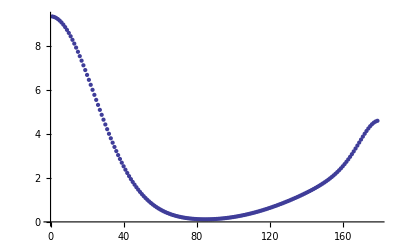

```mathematica
ListPlot[dσdΩ]
```

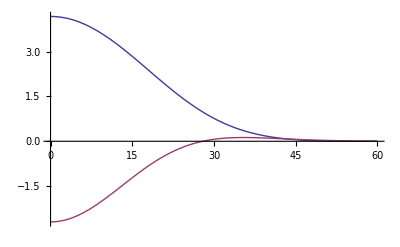

```mathematica
Plot[{Re[(4.18-I*2.70)*Exp[-(16-I*5.66)*4*0.66^2*Sin[t*Pi/360]^2]],Im[(4.18-I*2.70)*Exp[-(16-I*5.66)*4*0.66^2*Sin[t*Pi/360]^2]]},{t,0,60}]
```

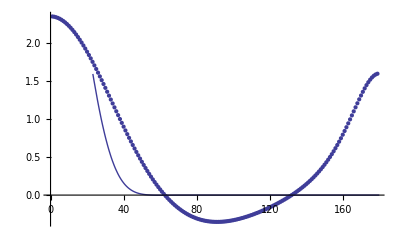

```mathematica
Show[ListPlot[Re[pp210]],Plot[Re[(4.18-I*2.70)*Exp[-(16-I*5.66)*4*0.66^2*Sin[t*Pi/360]^2]],{t,0,180}]]
```

```mathematica
Sqrt[.210^2+2*.210*m]
```

0.661947

```mathematica
θtoq[x_]:={2 Sqrt[.210^2+2*.210*m] Sin[x[[1]] Pi/360],x[[2]]}
```

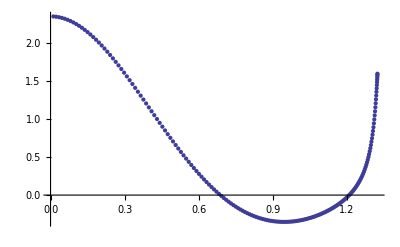

```mathematica
ListPlot[Re[θtoq/@pp210]]
```

{a→2.3714,b→4.5363}

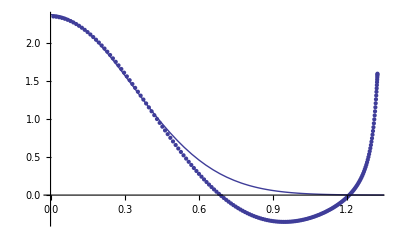

```mathematica
model=a Exp[-b*q^2];
FindFit[Re[θtoq/@pp210[[1;;40]]],model,{a,b},q,NormFunction->(Norm[Abs[#^2]]&)]
Show[ListPlot[Re[θtoq/@pp210]],Plot[Re[model/.%],{q,0,1.4}]]
```

FindFit::lmnl: The model a + b\ q + c\ q^2 + d\ q^3 + e\ q^4 + f\ q^5 + g\ q^6 + h\ q^7 + i\ q^8 is linear in the parameters {a, b, c, d, e, f, g, h, i}, but a nonlinear method or non-Euclidean norm was specified, so nonlinear methods will be used.

FindFit::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the norm of the residual. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{a→2.34905,b→0.0144824,c→-9.7791,d→1.79779,e→9.52228,f→1.92854,g→-3.58943,h→-4.62537,i→-3.50734}

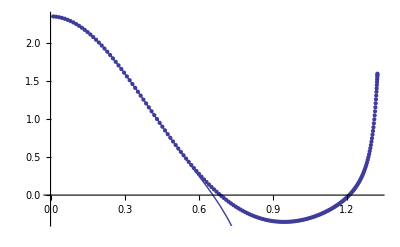

```mathematica
model=a +b Sin[q]+c Sin[2q]+d Sin[3 q];
FindFit[Re[θtoq/@pp210[[1;;40]]],model,{a,b,c,d,e,f,g,h,i},q,NormFunction->(Norm[Abs[#^2]]&)]
Show[ListPlot[Re[θtoq/@pp210]],Plot[Re[model/.%],{q,0,1.4}]]
```

```mathematica
Show[ListPlot[Re[θtoq/@pp210]],Plot[Re[(rea+I*ima) Exp[-(reb+I*imb)*q^2]/.%],{q,0,1.4}]]
```

-Graphics-

```mathematica
nij93pp210a=Import["/Users/Micah/Documents/JerryDuty/eikexp/nij93pp210a.csv"];
nij93pp210a=Transpose[{nij93pp210a[[All,1]],nij93pp210a[[All,2]]+I*nij93pp210a[[All,3]]}];
```

```mathematica
nij93pp210b=Import["/Users/Micah/Documents/JerryDuty/eikexp/nij93pp210b.csv"];
nij93pp210b=Transpose[{nij93pp210b[[All,1]],nij93pp210b[[All,2]]+I*nij93pp210b[[All,3]]}];
```

```mathematica
nij93pp210=Transpose[{nij93pp210a[[All,1]],nij93pp210a[[All,2]]+nij93pp210b[[All,2]]}];
```

```mathematica
nij93dσdΩ=Transpose[{nij93pp210[[All,1]],Abs[nij93pp210[[All,2]]]^2}];
```

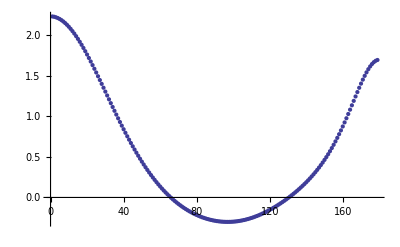

```mathematica
ListPlot[Re[nij93pp210]]
```

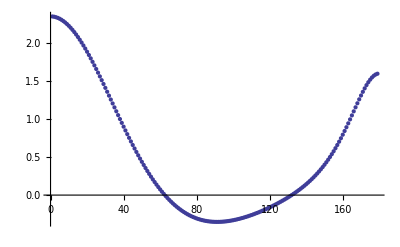

```mathematica
ListPlot[Re[pp210]]
```